# Functions of Multiple Variables

## Naman Taggar

```mathematica
save[name_]:=Export[NotebookDirectory[]<>"../../pages/posts/img/"<>name<>".png",%,ImageResolution->200]
```

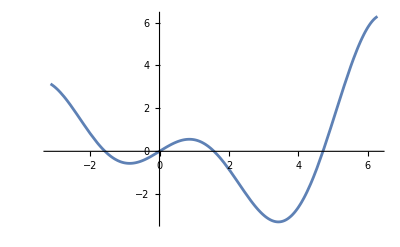

D:\11\website\resources\mm\../../pages/posts/img/mvc1.png

```mathematica
GraphicsColumn@{Plot[x Cos[x],{x,-π,2π}],
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2}]}
save["mvc1"]
```

```mathematica
Show[
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},PlotStyle->{Gray,Opacity[0.5]},BoxRatios->{1,1,1},Mesh->None,Lighting->"Neutral"],
ParametricPlot3D[{√5 Cos[t],√5 Sin[t],5},{t,-π,π},PlotStyle->Blue],
ParametricPlot3D[{√5 Cos[t],√5 Sin[t],0},{t,-π,π},PlotStyle->Red],
Graphics3D[{Blue,Opacity@0.3,InfinitePlane[{{0,0,5},{1,0,5},{0,1,5}}]}],
ViewPoint->{-5,7,1}
]
save["trace"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/trace.png

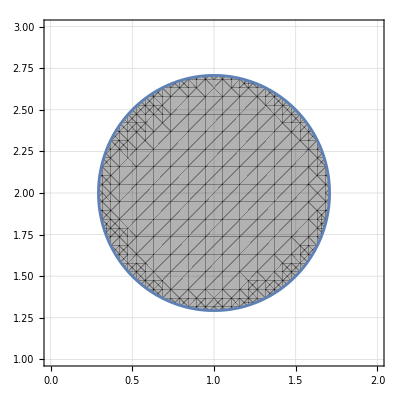

D:\11\website\resources\mm\../../pages/posts/img/openset2d.png

```mathematica
RegionPlot[(x-1)^2+(y-2)^2<=.5,{x,0,2},{y,1,3}, GridLines->Automatic, PlotStyle->{Directive[Black, Opacity[0.3]]}]
save["openset2d"]
```

```mathematica
{x0,y0} = {.3, .3};
Show[
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},3],ColorFunction->(GrayLevel[1.75-#3]&), PlotStyle->Directive[Opacity[0.65]],PlotPoints->200],
ParametricPlot3D[{x0+ .25Cos[t], y0+.25Sin[t],0}, {t, 0, 2Pi}, PlotStyle->Blue],
ParametricPlot3D[{x0+ .25Cos[t], y0+.25Sin[t],z},{t,0,2 Pi},{z,-.2, 1.1}, PlotStyle->Directive[{Blue, Opacity[0.2]}], Mesh->None],
Graphics3D[{
Red, Opacity[0.2],
InfinitePlane[{0, 0, .7}, {{1, 0, 0}, {0, 1, 0}}],
InfinitePlane[{0, 0, .9}, {{1, 0, 0}, {0, 1, 0}}]
}],PlotRange->{{-1, 1}, {-1, 1}, {-.2, 1.1}},BoxRatios->{1, 1, 1}, ViewPoint->{1.4, 2, 0.92}
]
save["limit"]
ClearAll[x0,y0]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/limit.png

```mathematica
Plot3D[Piecewise[{{(x y^2)/(x^2+y^4), x!=0||y!=0}, {0, True}}],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}, ViewPoint->{-1,1.2,0.85}]
save["discont"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/discont.png

```mathematica
Plot3D[1/(y-x^2),{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"},ViewPoint->{2,-1,1}]
save["para"]
```

-Graphics3D-

D:\11\website\resources\mm\../../pages/posts/img/para.png